```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.28;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.497145},{0.01,-0.493448},{0.02,-0.48987},{0.03,-0.4864},{0.04,-0.483036},{0.05,-0.479773},{0.06,-0.476608},{0.07,-0.473537},{0.08,-0.470556},{0.09,-0.467659},{0.1,-0.464844},{0.11,-0.462111},{0.12,-0.459445},{0.13,-0.456857},{0.14,-0.454329},{0.15,-0.45187},{0.16,-0.449465},{0.17,-0.447119},{0.18,-0.444824},{0.19,-0.442575},{0.2,-0.440376},{0.21,-0.438209},{0.22,-0.43609},{0.23,-0.433994},{0.24,-0.431932},{0.25,-0.429909},{0.26,-0.427897},{0.27,-0.425892},{0.28,-0.423924},{0.29,-0.421968},{0.3,-0.420001},{0.31,-0.418044},{0.32,-0.416105},{0.33,-0.414157},{0.34,-0.412182},{0.35,-0.41021},{0.36,-0.408236},{0.37,-0.406239},{0.38,-0.404199},{0.39,-0.402144},{0.4,-0.400073},{0.41,-0.397967},{0.42,-0.395807},{0.43,-0.393611},{0.44,-0.391371},{0.45,-0.389079},{0.46,-0.386735},{0.47,-0.384331},{0.48,-0.381864},{0.49,-0.37933},{0.5,-0.376724},{0.51,-0.374043},{0.52,-0.371279},{0.53,-0.368433},{0.54,-0.365494},{0.55,-0.362463},{0.56,-0.359331},{0.57,-0.356096},{0.58,-0.352752},{0.59,-0.349294},{0.6,-0.345718},{0.61,-0.342017},{0.62,-0.338188},{0.63,-0.334225},{0.64,-0.330122},{0.65,-0.325876},{0.66,-0.321478},{0.67,-0.316927},{0.68,-0.312214},{0.69,-0.307335},{0.7,-0.302285},{0.71,-0.297057},{0.72,-0.291646},{0.73,-0.286046},{0.74,-0.28025},{0.75,-0.274255},{0.76,-0.268053},{0.77,-0.261637},{0.78,-0.255004},{0.79,-0.248145},{0.8,-0.241054},{0.81,-0.233727},{0.82,-0.226156},{0.83,-0.218332},{0.84,-0.210255},{0.85,-0.20191},{0.86,-0.193297},{0.87,-0.184407},{0.88,-0.175231},{0.89,-0.165768},{0.9,-0.156},{0.91,-0.145934},{0.92,-0.135547},{0.93,-0.124847},{0.94,-0.113812},{0.95,-0.102446},{0.96,-0.0907309},{0.97,-0.0786673},{0.98,-0.0662384},{0.99,-0.0534406},{1.,-0.0402619}}

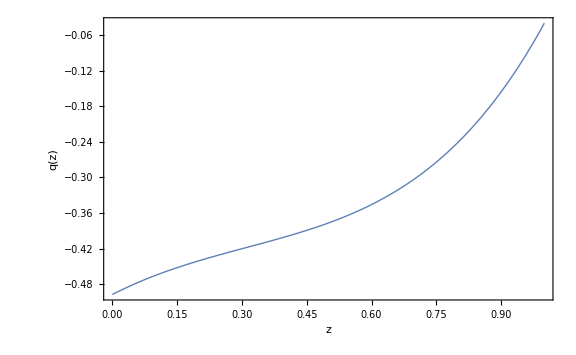

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.751738},{0.01,-0.735838},{0.02,-0.720222},{0.03,-0.704879},{0.04,-0.689805},{0.05,-0.674994},{0.06,-0.660439},{0.07,-0.646134},{0.08,-0.632073},{0.09,-0.61825},{0.1,-0.60466},{0.11,-0.591296},{0.12,-0.578154},{0.13,-0.565226},{0.14,-0.552512},{0.15,-0.54},{0.16,-0.527689},{0.17,-0.515576},{0.18,-0.50365},{0.19,-0.491913},{0.2,-0.480358},{0.21,-0.468976},{0.22,-0.45777},{0.23,-0.446733},{0.24,-0.435856},{0.25,-0.425143},{0.26,-0.414587},{0.27,-0.404179},{0.28,-0.393924},{0.29,-0.383815},{0.3,-0.373844},{0.31,-0.364011},{0.32,-0.354318},{0.33,-0.344758},{0.34,-0.33532},{0.35,-0.326006},{0.36,-0.316822},{0.37,-0.307758},{0.38,-0.298809},{0.39,-0.289967},{0.4,-0.281242},{0.41,-0.272631},{0.42,-0.264125},{0.43,-0.255719},{0.44,-0.24741},{0.45,-0.239208},{0.46,-0.231105},{0.47,-0.223097},{0.48,-0.215177},{0.49,-0.207343},{0.5,-0.199605},{0.51,-0.191957},{0.52,-0.184394},{0.53,-0.176911},{0.54,-0.169504},{0.55,-0.162178},{0.56,-0.154936},{0.57,-0.147772},{0.58,-0.140683},{0.59,-0.133663},{0.6,-0.12671},{0.61,-0.11983},{0.62,-0.113024},{0.63,-0.106287},{0.64,-0.0996168},{0.65,-0.0930089},{0.66,-0.0864608},{0.67,-0.0799779},{0.68,-0.0735573},{0.69,-0.0671974},{0.7,-0.0608961},{0.71,-0.0546537},{0.72,-0.048468},{0.73,-0.0423388},{0.74,-0.0362647},{0.75,-0.0302446},{0.76,-0.0242783},{0.77,-0.0183639},{0.78,-0.0125015},{0.79,-0.00668979},{0.8,-0.00092754},{0.81,0.00478492},{0.82,0.010449},{0.83,0.0160659},{0.84,0.0216358},{0.85,0.0271591},{0.86,0.0326369},{0.87,0.03807},{0.88,0.0434588},{0.89,0.0488038},{0.9,0.054106},{0.91,0.0593656},{0.92,0.0645831},{0.93,0.0697594},{0.94,0.0748949},{0.95,0.0799899},{0.96,0.0850449},{0.97,0.0900608},{0.98,0.0950377},{0.99,0.0999762},{1.,0.104877}}

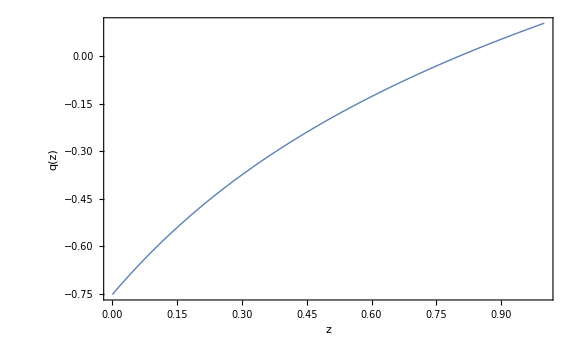

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.26092},{0.01,-1.20902},{0.02,-1.15894},{0.03,-1.11063},{0.04,-1.06402},{0.05,-1.01906},{0.06,-0.975682},{0.07,-0.933843},{0.08,-0.893472},{0.09,-0.85453},{0.1,-0.816951},{0.11,-0.780696},{0.12,-0.745703},{0.13,-0.711936},{0.14,-0.679337},{0.15,-0.647873},{0.16,-0.617488},{0.17,-0.588154},{0.18,-0.559818},{0.19,-0.53245},{0.2,-0.506016},{0.21,-0.48046},{0.22,-0.455761},{0.23,-0.431897},{0.24,-0.408831},{0.25,-0.386516},{0.26,-0.364932},{0.27,-0.344061},{0.28,-0.323867},{0.29,-0.304317},{0.3,-0.285395},{0.31,-0.267086},{0.32,-0.249352},{0.33,-0.23217},{0.34,-0.215528},{0.35,-0.19941},{0.36,-0.183788},{0.37,-0.168639},{0.38,-0.153952},{0.39,-0.139714},{0.4,-0.125909},{0.41,-0.112509},{0.42,-0.0995037},{0.43,-0.0868841},{0.44,-0.0746406},{0.45,-0.0627516},{0.46,-0.0511999},{0.47,-0.039978},{0.48,-0.0290786},{0.49,-0.0184938},{0.5,-0.00820487},{0.51,0.00180294},{0.52,0.0115353},{0.53,0.0209979},{0.54,0.0301967},{0.55,0.0391426},{0.56,0.047854},{0.57,0.0563357},{0.58,0.0645919},{0.59,0.0726271},{0.6,0.0804456},{0.61,0.0880608},{0.62,0.0954852},{0.63,0.102722},{0.64,0.109774},{0.65,0.116644},{0.66,0.123336},{0.67,0.129862},{0.68,0.13623},{0.69,0.142443},{0.7,0.148503},{0.71,0.154413},{0.72,0.160177},{0.73,0.165806},{0.74,0.171304},{0.75,0.176673},{0.76,0.181913},{0.77,0.187026},{0.78,0.192021},{0.79,0.196906},{0.8,0.20168},{0.81,0.206346},{0.82,0.210904},{0.83,0.215355},{0.84,0.219707},{0.85,0.223968},{0.86,0.228137},{0.87,0.232215},{0.88,0.236202},{0.89,0.2401},{0.9,0.243913},{0.91,0.247648},{0.92,0.251306},{0.93,0.254887},{0.94,0.258392},{0.95,0.26182},{0.96,0.265181},{0.97,0.268475},{0.98,0.271702},{0.99,0.274862},{1.,0.277956}}

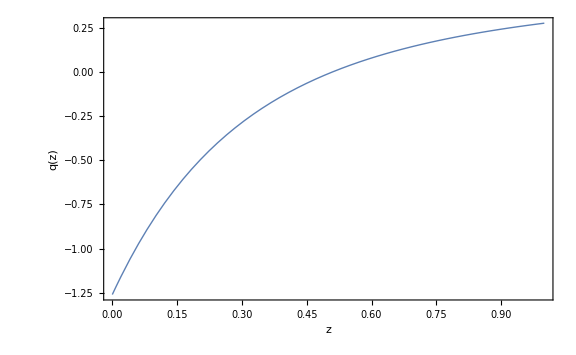

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.51552},{0.01,-1.43994},{0.02,-1.36782},{0.03,-1.29899},{0.04,-1.23328},{0.05,-1.17056},{0.06,-1.11068},{0.07,-1.05349},{0.08,-0.998883},{0.09,-0.946717},{0.1,-0.89687},{0.11,-0.849229},{0.12,-0.803691},{0.13,-0.760146},{0.14,-0.718491},{0.15,-0.67864},{0.16,-0.640505},{0.17,-0.603987},{0.18,-0.569029},{0.19,-0.535527},{0.2,-0.503435},{0.21,-0.472664},{0.22,-0.443159},{0.23,-0.414862},{0.24,-0.387701},{0.25,-0.361639},{0.26,-0.336607},{0.27,-0.312562},{0.28,-0.289466},{0.29,-0.267257},{0.3,-0.245904},{0.31,-0.225381},{0.32,-0.205617},{0.33,-0.186584},{0.34,-0.168261},{0.35,-0.150627},{0.36,-0.133649},{0.37,-0.117269},{0.38,-0.101465},{0.39,-0.0862217},{0.4,-0.0715241},{0.41,-0.057355},{0.42,-0.0436683},{0.43,-0.0304409},{0.44,-0.0176614},{0.45,-0.00531829},{0.46,0.00660208},{0.47,0.0181361},{0.48,0.0292995},{0.49,0.0401005},{0.5,0.0505475},{0.51,0.060652},{0.52,0.0704446},{0.53,0.0799352},{0.54,0.0891296},{0.55,0.0980339},{0.56,0.106664},{0.57,0.115041},{0.58,0.123169},{0.59,0.131051},{0.6,0.138693},{0.61,0.146116},{0.62,0.153329},{0.63,0.160337},{0.64,0.167141},{0.65,0.173744},{0.66,0.180167},{0.67,0.186418},{0.68,0.192499},{0.69,0.19841},{0.7,0.204155},{0.71,0.209744},{0.72,0.215192},{0.73,0.2205},{0.74,0.225669},{0.75,0.230699},{0.76,0.235592},{0.77,0.240366},{0.78,0.245024},{0.79,0.249565},{0.8,0.25399},{0.81,0.2583},{0.82,0.26251},{0.83,0.266621},{0.84,0.270634},{0.85,0.274547},{0.86,0.278362},{0.87,0.28209},{0.88,0.285737},{0.89,0.2893},{0.9,0.29278},{0.91,0.296175},{0.92,0.299494},{0.93,0.302743},{0.94,0.30592},{0.95,0.309026},{0.96,0.312059},{0.97,0.315031},{0.98,0.317941},{0.99,0.320788},{1.,0.32357}}

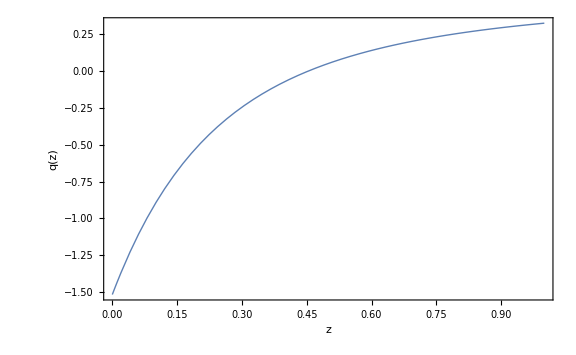

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

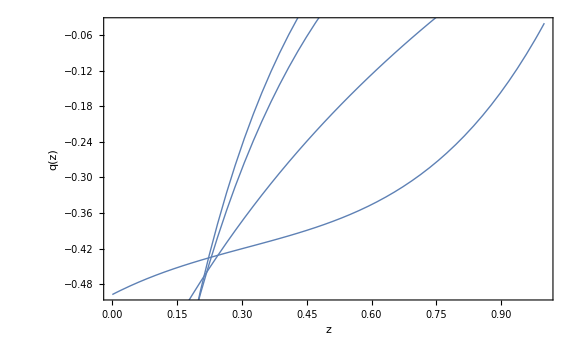

```mathematica
Show[p04n, p02n, p02, p04]
```

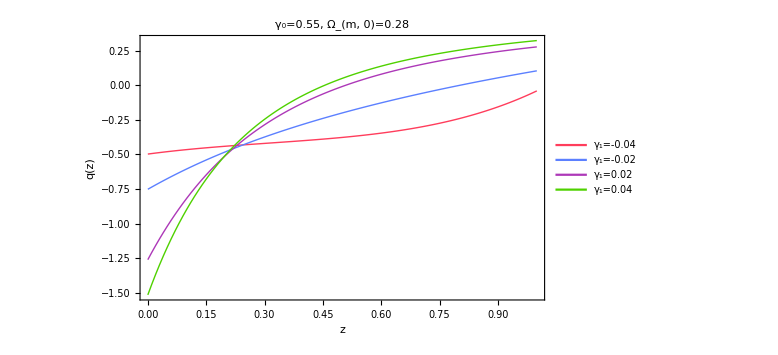

```mathematica
list2=ListLinePlot[{points1,points2,points3, points4}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Thick, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["q(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.28", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points11=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.469447},{0.01,-0.465316},{0.02,-0.461302},{0.03,-0.457395},{0.04,-0.45359},{0.05,-0.449885},{0.06,-0.446277},{0.07,-0.44276},{0.08,-0.439331},{0.09,-0.435985},{0.1,-0.432718},{0.11,-0.429532},{0.12,-0.426411},{0.13,-0.423366},{0.14,-0.420379},{0.15,-0.41746},{0.16,-0.414593},{0.17,-0.411784},{0.18,-0.409024},{0.19,-0.406309},{0.2,-0.403642},{0.21,-0.401007},{0.22,-0.398418},{0.23,-0.395851},{0.24,-0.393319},{0.25,-0.390823},{0.26,-0.388339},{0.27,-0.385862},{0.28,-0.383421},{0.29,-0.380992},{0.3,-0.378553},{0.31,-0.376125},{0.32,-0.373713},{0.33,-0.371295},{0.34,-0.368851},{0.35,-0.366411},{0.36,-0.363971},{0.37,-0.361509},{0.38,-0.359008},{0.39,-0.356494},{0.4,-0.353966},{0.41,-0.351406},{0.42,-0.348797},{0.43,-0.346154},{0.44,-0.343473},{0.45,-0.340744},{0.46,-0.337967},{0.47,-0.335137},{0.48,-0.33225},{0.49,-0.329302},{0.5,-0.326289},{0.51,-0.323207},{0.52,-0.320052},{0.53,-0.316822},{0.54,-0.313509},{0.55,-0.310112},{0.56,-0.306625},{0.57,-0.303046},{0.58,-0.299368},{0.59,-0.295589},{0.6,-0.291704},{0.61,-0.287708},{0.62,-0.283598},{0.63,-0.279368},{0.64,-0.275013},{0.65,-0.270531},{0.66,-0.265915},{0.67,-0.261162},{0.68,-0.256267},{0.69,-0.251224},{0.7,-0.24603},{0.71,-0.240679},{0.72,-0.235167},{0.73,-0.229488},{0.74,-0.223637},{0.75,-0.217611},{0.76,-0.211403},{0.77,-0.205008},{0.78,-0.198422},{0.79,-0.191639},{0.8,-0.184653},{0.81,-0.17746},{0.82,-0.170055},{0.83,-0.162429},{0.84,-0.154582},{0.85,-0.146502},{0.86,-0.138189},{0.87,-0.129634},{0.88,-0.120831},{0.89,-0.111778},{0.9,-0.102461},{0.91,-0.092884},{0.92,-0.0830287},{0.93,-0.0729021},{0.94,-0.0624837},{0.95,-0.0517795},{0.96,-0.0407708},{0.97,-0.0294602},{0.98,-0.0178322},{0.99,-0.00588381},{1.,0.00639567}}

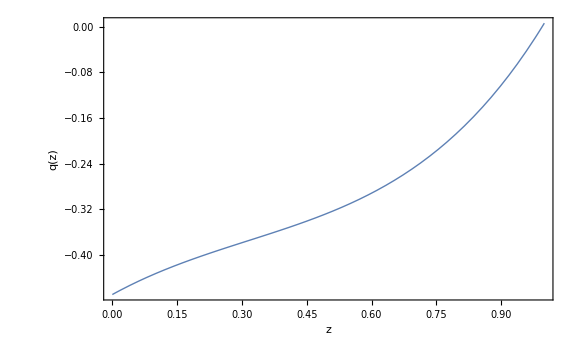

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points22=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.690827},{0.01,-0.675469},{0.02,-0.660393},{0.03,-0.645588},{0.04,-0.63105},{0.05,-0.616771},{0.06,-0.602746},{0.07,-0.588968},{0.08,-0.57543},{0.09,-0.562127},{0.1,-0.549052},{0.11,-0.536201},{0.12,-0.523566},{0.13,-0.511144},{0.14,-0.498926},{0.15,-0.486913},{0.16,-0.475092},{0.17,-0.463464},{0.18,-0.452024},{0.19,-0.440762},{0.2,-0.429681},{0.21,-0.418771},{0.22,-0.408027},{0.23,-0.39745},{0.24,-0.387033},{0.25,-0.376768},{0.26,-0.36666},{0.27,-0.356699},{0.28,-0.346878},{0.29,-0.337204},{0.3,-0.327667},{0.31,-0.318259},{0.32,-0.308985},{0.33,-0.299842},{0.34,-0.290824},{0.35,-0.281921},{0.36,-0.273137},{0.37,-0.264476},{0.38,-0.255928},{0.39,-0.247487},{0.4,-0.239148},{0.41,-0.230921},{0.42,-0.222801},{0.43,-0.21478},{0.44,-0.206853},{0.45,-0.199017},{0.46,-0.191283},{0.47,-0.183643},{0.48,-0.176092},{0.49,-0.168625},{0.5,-0.161238},{0.51,-0.153942},{0.52,-0.146731},{0.53,-0.139601},{0.54,-0.132546},{0.55,-0.125564},{0.56,-0.118657},{0.57,-0.111829},{0.58,-0.105076},{0.59,-0.0983938},{0.6,-0.0917777},{0.61,-0.0852249},{0.62,-0.0787396},{0.63,-0.0723242},{0.64,-0.065975},{0.65,-0.0596888},{0.66,-0.0534623},{0.67,-0.0472929},{0.68,-0.0411833},{0.69,-0.0351337},{0.7,-0.0291416},{0.71,-0.0232052},{0.72,-0.0173245},{0.73,-0.0114977},{0.74,-0.00572448},{0.75,-3.35809×10^-6},{0.76,0.00566607},{0.77,0.0112849},{0.78,0.016854},{0.79,0.0223739},{0.8,0.0278461},{0.81,0.0332704},{0.82,0.0386477},{0.83,0.0439795},{0.84,0.049266},{0.85,0.0545075},{0.86,0.059705},{0.87,0.0648594},{0.88,0.0699709},{0.89,0.0750402},{0.9,0.0800681},{0.91,0.0850549},{0.92,0.0900012},{0.93,0.0949075},{0.94,0.0997745},{0.95,0.104602},{0.96,0.109392},{0.97,0.114143},{0.98,0.118857},{0.99,0.123534},{1.,0.128174}}

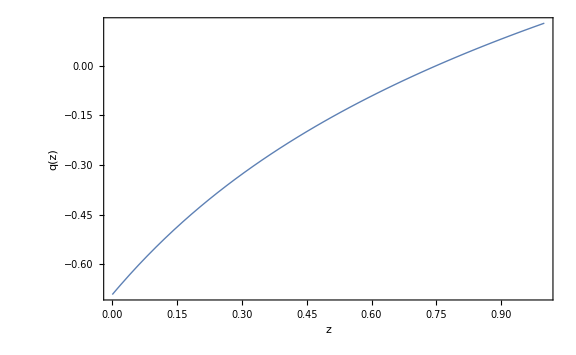

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points33=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.17242},{0.01,-1.12256},{0.02,-1.0745},{0.03,-1.02817},{0.04,-0.983509},{0.05,-0.940457},{0.06,-0.898955},{0.07,-0.858946},{0.08,-0.820366},{0.09,-0.783174},{0.1,-0.747302},{0.11,-0.712715},{0.12,-0.679348},{0.13,-0.647166},{0.14,-0.616112},{0.15,-0.586152},{0.16,-0.557235},{0.17,-0.529323},{0.18,-0.502379},{0.19,-0.476359},{0.2,-0.451239},{0.21,-0.426967},{0.22,-0.403511},{0.23,-0.380848},{0.24,-0.358957},{0.25,-0.337788},{0.26,-0.317314},{0.27,-0.297517},{0.28,-0.278374},{0.29,-0.259846},{0.3,-0.241914},{0.31,-0.224561},{0.32,-0.207767},{0.33,-0.191498},{0.34,-0.175738},{0.35,-0.160473},{0.36,-0.14569},{0.37,-0.131356},{0.38,-0.117457},{0.39,-0.103983},{0.4,-0.0909221},{0.41,-0.0782528},{0.42,-0.0659548},{0.43,-0.0540196},{0.44,-0.0424381},{0.45,-0.031201},{0.46,-0.0202856},{0.47,-0.00967957},{0.48,0.000623975},{0.49,0.0106319},{0.5,0.0203517},{0.51,0.0298027},{0.52,0.0389962},{0.53,0.0479373},{0.54,0.0566312},{0.55,0.0650835},{0.56,0.073305},{0.57,0.0813123},{0.58,0.0891093},{0.59,0.0967},{0.6,0.104088},{0.61,0.111278},{0.62,0.118284},{0.63,0.125114},{0.64,0.13177},{0.65,0.138256},{0.66,0.144575},{0.67,0.150735},{0.68,0.156746},{0.69,0.16261},{0.7,0.168331},{0.71,0.173908},{0.72,0.179347},{0.73,0.184659},{0.74,0.189848},{0.75,0.194915},{0.76,0.199861},{0.77,0.204687},{0.78,0.209399},{0.79,0.214006},{0.8,0.218511},{0.81,0.222914},{0.82,0.227216},{0.83,0.231419},{0.84,0.235524},{0.85,0.239542},{0.86,0.243475},{0.87,0.247321},{0.88,0.251083},{0.89,0.25476},{0.9,0.258359},{0.91,0.261884},{0.92,0.265335},{0.93,0.268714},{0.94,0.272019},{0.95,0.275253},{0.96,0.278424},{0.97,0.281532},{0.98,0.284576},{0.99,0.287558},{1.,0.290477}}

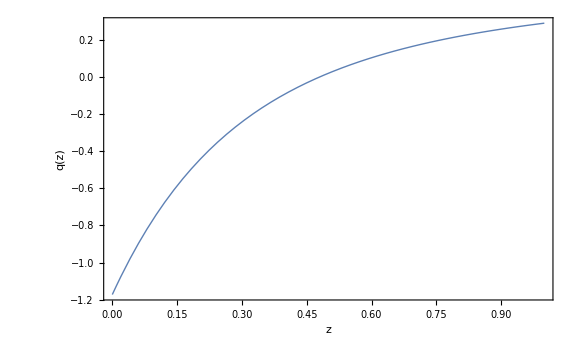

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points44=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.41321},{0.01,-1.34076},{0.02,-1.27167},{0.03,-1.20579},{0.04,-1.14295},{0.05,-1.08302},{0.06,-1.02583},{0.07,-0.971256},{0.08,-0.919175},{0.09,-0.869452},{0.1,-0.821964},{0.11,-0.776608},{0.12,-0.733273},{0.13,-0.691851},{0.14,-0.652256},{0.15,-0.614379},{0.16,-0.578159},{0.17,-0.543482},{0.18,-0.510298},{0.19,-0.478513},{0.2,-0.448064},{0.21,-0.418893},{0.22,-0.390919},{0.23,-0.364102},{0.24,-0.338372},{0.25,-0.313677},{0.26,-0.289979},{0.27,-0.267213},{0.28,-0.245343},{0.29,-0.224333},{0.3,-0.204126},{0.31,-0.184696},{0.32,-0.166026},{0.33,-0.148038},{0.34,-0.130706},{0.35,-0.114012},{0.36,-0.0979365},{0.37,-0.0824601},{0.38,-0.0675544},{0.39,-0.0531625},{0.4,-0.0392697},{0.41,-0.0258629},{0.42,-0.0129285},{0.43,-0.000451379},{0.44,0.0116093},{0.45,0.0232724},{0.46,0.0345472},{0.47,0.0454434},{0.48,0.0559706},{0.49,0.0661567},{0.5,0.0760228},{0.51,0.085575},{0.52,0.09482},{0.53,0.103767},{0.54,0.112443},{0.55,0.120855},{0.56,0.129009},{0.57,0.13691},{0.58,0.144569},{0.59,0.152008},{0.6,0.159231},{0.61,0.166241},{0.62,0.173042},{0.63,0.179642},{0.64,0.186062},{0.65,0.192305},{0.66,0.198373},{0.67,0.204267},{0.68,0.209992},{0.69,0.215567},{0.7,0.220996},{0.71,0.226278},{0.72,0.231415},{0.73,0.236413},{0.74,0.241286},{0.75,0.246036},{0.76,0.250662},{0.77,0.255165},{0.78,0.259551},{0.79,0.263834},{0.8,0.268013},{0.81,0.272088},{0.82,0.276059},{0.83,0.279928},{0.84,0.28371},{0.85,0.287405},{0.86,0.291014},{0.87,0.294535},{0.88,0.297969},{0.89,0.301322},{0.9,0.304605},{0.91,0.307816},{0.92,0.310954},{0.93,0.314018},{0.94,0.317009},{0.95,0.319937},{0.96,0.322805},{0.97,0.325612},{0.98,0.328357},{0.99,0.331038},{1.,0.333667}}

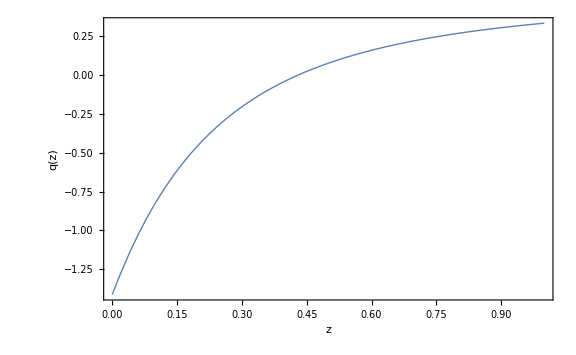

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

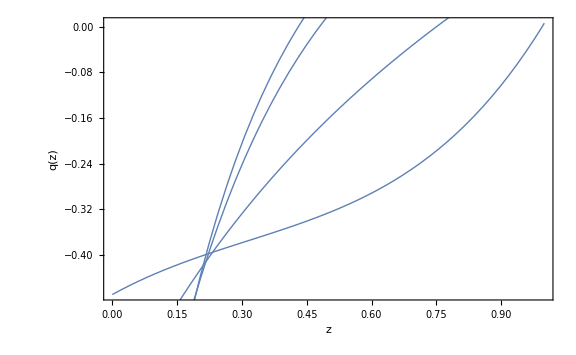

```mathematica
Show[p04n, p02n, p02, p04]
```

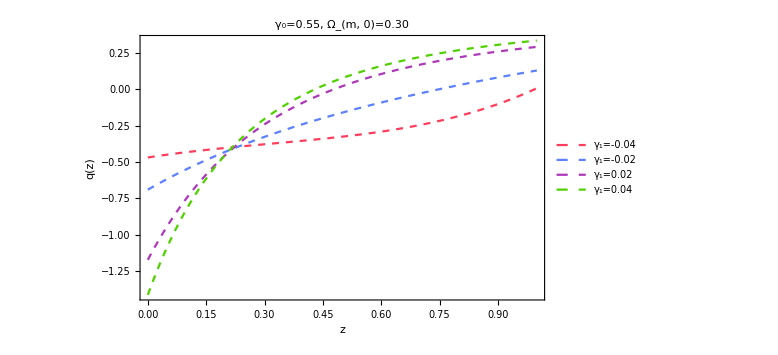

```mathematica
list3=ListLinePlot[{points11,points22,points33, points44}, PlotStyle->{{Dashed, RGBColor[1,0.24,0.36]}, {Dashed, RGBColor[0.36,0.5,1]}, {Dashed, RGBColor[0.68,0.22,0.72]}, {Dashed, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["q(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.30", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points111=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.450033},{0.01,-0.446444},{0.02,-0.442969},{0.03,-0.439596},{0.04,-0.436322},{0.05,-0.433142},{0.06,-0.430055},{0.07,-0.427056},{0.08,-0.42414},{0.09,-0.421304},{0.1,-0.418542},{0.11,-0.415857},{0.12,-0.413234},{0.13,-0.410683},{0.14,-0.408186},{0.15,-0.405754},{0.16,-0.403368},{0.17,-0.40104},{0.18,-0.398754},{0.19,-0.396513},{0.2,-0.394314},{0.21,-0.392145},{0.22,-0.390017},{0.23,-0.387906},{0.24,-0.385832},{0.25,-0.383787},{0.26,-0.381745},{0.27,-0.379717},{0.28,-0.377719},{0.29,-0.375725},{0.3,-0.373716},{0.31,-0.371725},{0.32,-0.369742},{0.33,-0.367742},{0.34,-0.365717},{0.35,-0.3637},{0.36,-0.361673},{0.37,-0.359615},{0.38,-0.357519},{0.39,-0.355414},{0.4,-0.353285},{0.41,-0.351115},{0.42,-0.348895},{0.43,-0.346641},{0.44,-0.344341},{0.45,-0.341991},{0.46,-0.339588},{0.47,-0.337128},{0.48,-0.334606},{0.49,-0.332019},{0.5,-0.329361},{0.51,-0.326631},{0.52,-0.323821},{0.53,-0.320932},{0.54,-0.317955},{0.55,-0.314888},{0.56,-0.311727},{0.57,-0.308466},{0.58,-0.305102},{0.59,-0.301629},{0.6,-0.298045},{0.61,-0.294344},{0.62,-0.290521},{0.63,-0.286571},{0.64,-0.282491},{0.65,-0.278275},{0.66,-0.273918},{0.67,-0.269417},{0.68,-0.264765},{0.69,-0.259958},{0.7,-0.254991},{0.71,-0.249857},{0.72,-0.244555},{0.73,-0.239076},{0.74,-0.233417},{0.75,-0.227572},{0.76,-0.221535},{0.77,-0.215302},{0.78,-0.208867},{0.79,-0.202224},{0.8,-0.195366},{0.81,-0.188292},{0.82,-0.180993},{0.83,-0.173461},{0.84,-0.165697},{0.85,-0.157687},{0.86,-0.149432},{0.87,-0.140922},{0.88,-0.13215},{0.89,-0.123116},{0.9,-0.113803},{0.91,-0.104217},{0.92,-0.0943382},{0.93,-0.0841736},{0.94,-0.0737025},{0.95,-0.0629307},{0.96,-0.0518393},{0.97,-0.0404302},{0.98,-0.0286884},{0.99,-0.01661},{1.,-0.00418454}}

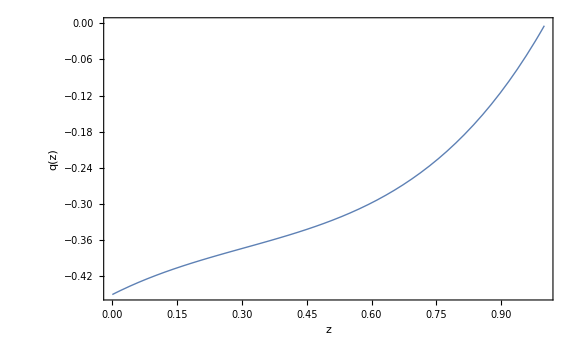

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points222=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-0.690827},{0.01,-0.675469},{0.02,-0.660393},{0.03,-0.645588},{0.04,-0.63105},{0.05,-0.616771},{0.06,-0.602746},{0.07,-0.588968},{0.08,-0.57543},{0.09,-0.562127},{0.1,-0.549052},{0.11,-0.536201},{0.12,-0.523566},{0.13,-0.511144},{0.14,-0.498926},{0.15,-0.486913},{0.16,-0.475092},{0.17,-0.463464},{0.18,-0.452024},{0.19,-0.440762},{0.2,-0.429681},{0.21,-0.418771},{0.22,-0.408027},{0.23,-0.39745},{0.24,-0.387033},{0.25,-0.376768},{0.26,-0.36666},{0.27,-0.356699},{0.28,-0.346878},{0.29,-0.337204},{0.3,-0.327667},{0.31,-0.318259},{0.32,-0.308985},{0.33,-0.299842},{0.34,-0.290824},{0.35,-0.281921},{0.36,-0.273137},{0.37,-0.264476},{0.38,-0.255928},{0.39,-0.247487},{0.4,-0.239148},{0.41,-0.230921},{0.42,-0.222801},{0.43,-0.21478},{0.44,-0.206853},{0.45,-0.199017},{0.46,-0.191283},{0.47,-0.183643},{0.48,-0.176092},{0.49,-0.168625},{0.5,-0.161238},{0.51,-0.153942},{0.52,-0.146731},{0.53,-0.139601},{0.54,-0.132546},{0.55,-0.125564},{0.56,-0.118657},{0.57,-0.111829},{0.58,-0.105076},{0.59,-0.0983938},{0.6,-0.0917777},{0.61,-0.0852249},{0.62,-0.0787396},{0.63,-0.0723242},{0.64,-0.065975},{0.65,-0.0596888},{0.66,-0.0534623},{0.67,-0.0472929},{0.68,-0.0411833},{0.69,-0.0351337},{0.7,-0.0291416},{0.71,-0.0232052},{0.72,-0.0173245},{0.73,-0.0114977},{0.74,-0.00572448},{0.75,-3.35809×10^-6},{0.76,0.00566607},{0.77,0.0112849},{0.78,0.016854},{0.79,0.0223739},{0.8,0.0278461},{0.81,0.0332704},{0.82,0.0386477},{0.83,0.0439795},{0.84,0.049266},{0.85,0.0545075},{0.86,0.059705},{0.87,0.0648594},{0.88,0.0699709},{0.89,0.0750402},{0.9,0.0800681},{0.91,0.0850549},{0.92,0.0900012},{0.93,0.0949075},{0.94,0.0997745},{0.95,0.104602},{0.96,0.109392},{0.97,0.114143},{0.98,0.118857},{0.99,0.123534},{1.,0.128174}}

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points333=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.17242},{0.01,-1.12256},{0.02,-1.0745},{0.03,-1.02817},{0.04,-0.983509},{0.05,-0.940457},{0.06,-0.898955},{0.07,-0.858946},{0.08,-0.820366},{0.09,-0.783174},{0.1,-0.747302},{0.11,-0.712715},{0.12,-0.679348},{0.13,-0.647166},{0.14,-0.616112},{0.15,-0.586152},{0.16,-0.557235},{0.17,-0.529323},{0.18,-0.502379},{0.19,-0.476359},{0.2,-0.451239},{0.21,-0.426967},{0.22,-0.403511},{0.23,-0.380848},{0.24,-0.358957},{0.25,-0.337788},{0.26,-0.317314},{0.27,-0.297517},{0.28,-0.278374},{0.29,-0.259846},{0.3,-0.241914},{0.31,-0.224561},{0.32,-0.207767},{0.33,-0.191498},{0.34,-0.175738},{0.35,-0.160473},{0.36,-0.14569},{0.37,-0.131356},{0.38,-0.117457},{0.39,-0.103983},{0.4,-0.0909221},{0.41,-0.0782528},{0.42,-0.0659548},{0.43,-0.0540196},{0.44,-0.0424381},{0.45,-0.031201},{0.46,-0.0202856},{0.47,-0.00967957},{0.48,0.000623975},{0.49,0.0106319},{0.5,0.0203517},{0.51,0.0298027},{0.52,0.0389962},{0.53,0.0479373},{0.54,0.0566312},{0.55,0.0650835},{0.56,0.073305},{0.57,0.0813123},{0.58,0.0891093},{0.59,0.0967},{0.6,0.104088},{0.61,0.111278},{0.62,0.118284},{0.63,0.125114},{0.64,0.13177},{0.65,0.138256},{0.66,0.144575},{0.67,0.150735},{0.68,0.156746},{0.69,0.16261},{0.7,0.168331},{0.71,0.173908},{0.72,0.179347},{0.73,0.184659},{0.74,0.189848},{0.75,0.194915},{0.76,0.199861},{0.77,0.204687},{0.78,0.209399},{0.79,0.214006},{0.8,0.218511},{0.81,0.222914},{0.82,0.227216},{0.83,0.231419},{0.84,0.235524},{0.85,0.239542},{0.86,0.243475},{0.87,0.247321},{0.88,0.251083},{0.89,0.25476},{0.9,0.258359},{0.91,0.261884},{0.92,0.265335},{0.93,0.268714},{0.94,0.272019},{0.95,0.275253},{0.96,0.278424},{0.97,0.281532},{0.98,0.284576},{0.99,0.287558},{1.,0.290477}}

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

-Graphics-

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.32;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points444=Table[{z,q[z]},{z,0,1,0.01}]
```

{{0.,-1.35855},{0.01,-1.28622},{0.02,-1.21734},{0.03,-1.15173},{0.04,-1.08923},{0.05,-1.02968},{0.06,-0.972941},{0.07,-0.918856},{0.08,-0.867302},{0.09,-0.818142},{0.1,-0.771248},{0.11,-0.726513},{0.12,-0.683821},{0.13,-0.643061},{0.14,-0.604144},{0.15,-0.566958},{0.16,-0.531438},{0.17,-0.49747},{0.18,-0.464998},{0.19,-0.43393},{0.2,-0.404199},{0.21,-0.375745},{0.22,-0.348487},{0.23,-0.322382},{0.24,-0.297359},{0.25,-0.273367},{0.26,-0.250365},{0.27,-0.228288},{0.28,-0.2071},{0.29,-0.186763},{0.3,-0.16722},{0.31,-0.148445},{0.32,-0.130419},{0.33,-0.113066},{0.34,-0.0963598},{0.35,-0.080281},{0.36,-0.0648096},{0.37,-0.049926},{0.38,-0.0356017},{0.39,-0.0217814},{0.4,-0.00844997},{0.41,0.00440618},{0.42,0.0168009},{0.43,0.0287498},{0.44,0.0402922},{0.45,0.0514469},{0.46,0.0622235},{0.47,0.0726318},{0.48,0.0826819},{0.49,0.0924006},{0.5,0.101808},{0.51,0.110912},{0.52,0.119718},{0.53,0.128236},{0.54,0.13649},{0.55,0.14449},{0.56,0.152241},{0.57,0.159747},{0.58,0.16702},{0.59,0.174081},{0.6,0.180934},{0.61,0.187581},{0.62,0.194027},{0.63,0.20028},{0.64,0.206361},{0.65,0.21227},{0.66,0.218012},{0.67,0.223587},{0.68,0.229},{0.69,0.234269},{0.7,0.239398},{0.71,0.244386},{0.72,0.249236},{0.73,0.253952},{0.74,0.25855},{0.75,0.263029},{0.76,0.26739},{0.77,0.271635},{0.78,0.275767},{0.79,0.2798},{0.8,0.283735},{0.81,0.28757},{0.82,0.291307},{0.83,0.294947},{0.84,0.298503},{0.85,0.301978},{0.86,0.305369},{0.87,0.308678},{0.88,0.311903},{0.89,0.315052},{0.9,0.318134},{0.91,0.321148},{0.92,0.324093},{0.93,0.326968},{0.94,0.329773},{0.95,0.332518},{0.96,0.335207},{0.97,0.337838},{0.98,0.34041},{0.99,0.342922},{1.,0.345384}}

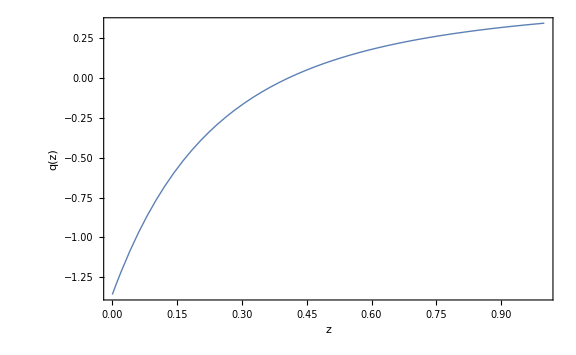

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

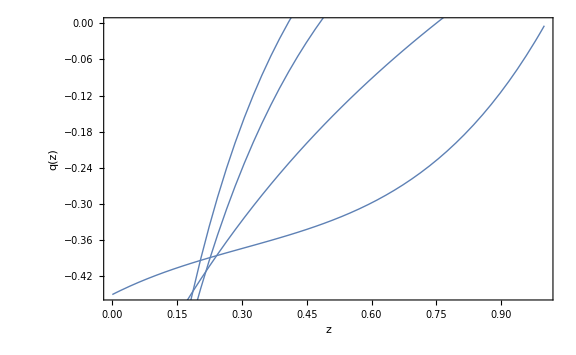

```mathematica
Show[p04n, p02n, p02, p04]
```

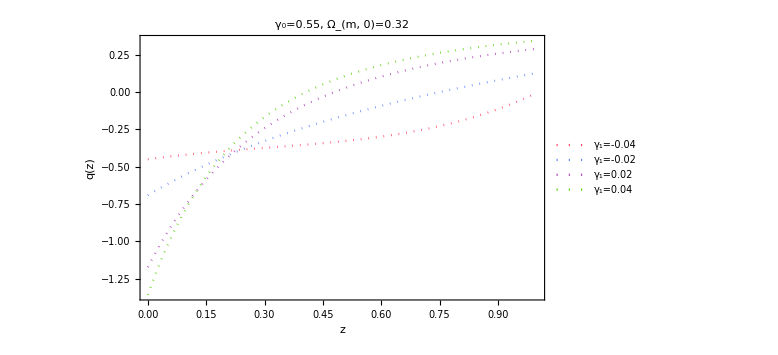

```mathematica
list4=ListLinePlot[{points111,points222,points333, points444}, PlotStyle->{{Dotted, RGBColor[1,0.24,0.36]}, {Dotted, RGBColor[0.36,0.5,1]}, {Dotted, RGBColor[0.68,0.22,0.72]}, {Dotted, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["q(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55, Ω_(m, 0)=0.32", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

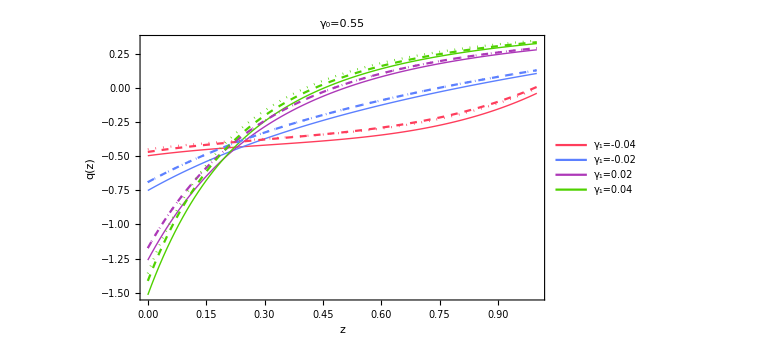

```mathematica
list5=ListLinePlot[{points1,points2,points3, points4, points11,points22,points33, points44, points111,points222,points333, points444}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick, RGBColor[0.36,0.5,1]}, {Thick, RGBColor[0.68,0.22,0.72]}, {Thick, RGBColor[0.31,0.82,0]}, {Dashed, RGBColor[1,0.24,0.36]}, {Dashed, RGBColor[0.36,0.5,1]}, {Dashed, RGBColor[0.68,0.22,0.72]}, {Dashed, RGBColor[0.31,0.82,0]},{Dotted, RGBColor[1,0.24,0.36]}, {Dotted, RGBColor[0.36,0.5,1]}, {Dotted, RGBColor[0.68,0.22,0.72]}, {Dotted, RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["q(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"γ_1=-0.04", "γ_1=-0.02", "γ_1=0.02", "γ_1=0.04"}, Background->White],{Right,Bottom}], PlotLabel->Style["γ_0=0.55", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
SetDirectory["G:\\My Drive\\U\\paper"]
```

G:\My Drive\U\paper

```mathematica
Export["q(z)_om028.pdf",list2,ImageResolution->500]
```

q(z)_om028.pdf

```mathematica
Export["q(z)_om030.pdf",list3,ImageResolution->500]
```

q(z)_om030.pdf

```mathematica
Export["q(z)_om032.pdf",list4,ImageResolution->500]
```

q(z)_om032.pdf

```mathematica
Export["q(z)_all.pdf",list5,ImageResolution->500]
```

q(z)_all.pdf